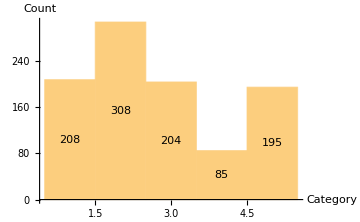

```mathematica
weights={200,300,200,100,200};
categories=Range[1,Length[weights]];
dist=EmpiricalDistribution[weights->categories];
data=RandomVariate[dist,1000];
Histogram[data,LabelingFunction-> Center,AxesLabel->{"Category","Count"}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/sampling_from_discrete_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\sampling_from_discrete_distribution.pdf

```mathematica
doors= Range[3];
doorsWithPrize=RandomChoice[doors,1000];
firstChoice=RandomChoice[doors,Length[doorsWithPrize]];
doorsWithoutPrize=MapThread[RandomChoice[Complement[doors,{#1,#2}]]&,{doorsWithPrize,firstChoice}];
secondChoice=MapThread[RandomChoice[Complement[doors,{#1,#2}]]&,{doorsWithoutPrize,firstChoice}];
ProbabilityWinningPrize[choice_]:=Apply[Plus,MapThread[Boole[#1==#2]&,{doorsWithPrize,choice}]]/Length[doorsWithPrize]//N;
Print["Probability of winning by staying with your first choice = ",ProbabilityWinningPrize[firstChoice]];
Print["Probability of winning by choosing the remaining door = ",ProbabilityWinningPrize[secondChoice]];
```

Probability of winning by staying with your first choice = 0.339

Probability of winning by choosing the remaining door = 0.661

```mathematica
dist=TransformedDistribution[x^2,x\[Distributed]NormalDistribution[0,σ]];
PDF[dist,y]
```

Piecewise[{{(ⅇ^(-y/(2 σ^2)))/(√(2 π) √y σ), y>0}, {0, y<0}, {Indeterminate, True}}]

```mathematica
TransformedDistribution[u+v,{u\[Distributed]PoissonDistribution[λ1],v\[Distributed]PoissonDistribution[λ2]}]
```

PoissonDistribution[λ1+λ2]

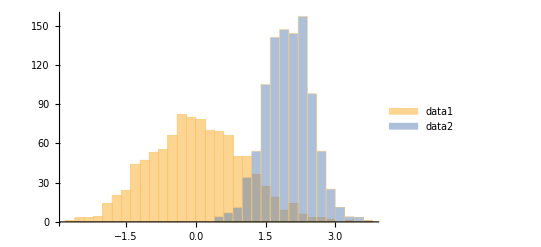

```mathematica
data1=RandomVariate[NormalDistribution[0,1], 1000];
data2=RandomVariate[NormalDistribution[2,0.5], 1000];
Histogram[{data1,data2}, ChartLegends->{"data1","data2"}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/normal_distributions_from_data.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\normal_distributions_from_data.pdf

```mathematica
Histogram3D[RandomVariate[BinormalDistribution[0],10000]]
```

-Graphics3D-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/histogram_3d.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\histogram_3d.pdf

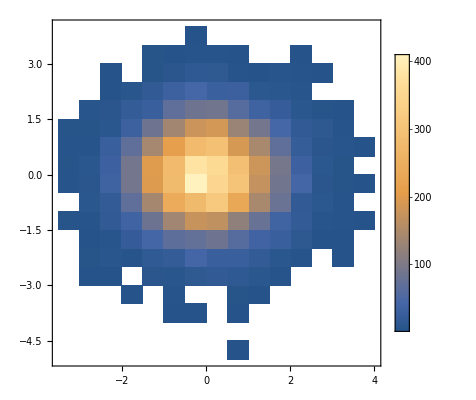

```mathematica
DensityHistogram[RandomVariate[BinormalDistribution[0],10000], ChartLegends->Automatic]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/density_histogram.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\density_histogram.pdf

```mathematica
dist=ProbabilityDistribution[Sqrt[2]/Pi/α/(1+(x/α)^4),{x,-Infinity,Infinity}, Assumptions->{α>0}];
(* dist=ProbabilityDistribution[1/(1+x^4),{x,-Infinity,Infinity},Method->"Normalize"];*)
```

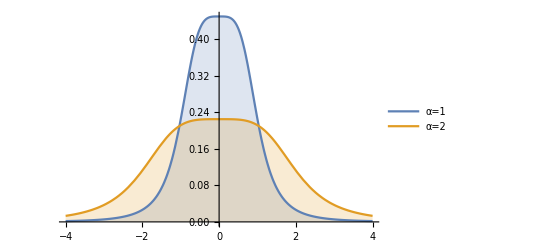

```mathematica
Plot[{PDF[dist,x]//.{α->1},
PDF[dist,x]//.{α->2}},{x,-4,4},Filling->Axis, PlotLegends->Placed[{"α=1","α=2"},Right]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/probability_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\probability_distribution.pdf

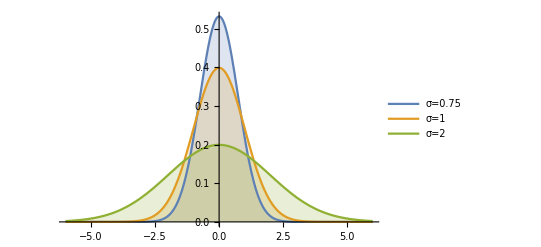

```mathematica
Plot[Table[PDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}]//Evaluate,{x,-6,6},Filling->Axis,PlotLegends->Placed[{"σ=0.75","σ=1","σ=2"},Right]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/normal_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\normal_distribution.pdf

```mathematica
Plot3D[PDF[MultinormalDistribution[{0,0},{{2,1},{1,2}}],{x,y}],{x,-4,4},{y,-4,4}, PlotPoints->{50,50}]
```

-Graphics3D-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/multi_normal_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\multi_normal_distribution.pdf

```mathematica
dist=ProbabilityDistribution[Gamma[3/4]/(Gamma[5/4]*Sqrt[2 Pi^3])/(1+x^4+y^4),{x,-Infinity,Infinity},{y,-Infinity,Infinity}];
```

```mathematica
Plot3D[PDF[dist,{x,y}],{x,-4,4},{y,-4,4},PlotRange->{0,0.2},PlotPoints->{50,50}]
```

-Graphics3D-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/joint_probability_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\joint_probability_distribution.pdf

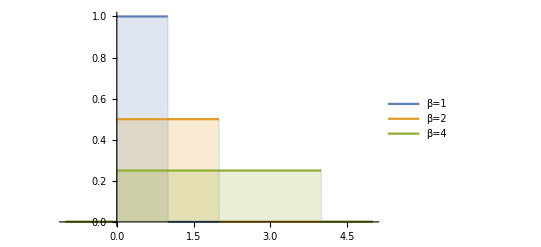

```mathematica
Plot[Table[PDF[UniformDistribution[{0, β}],x],{β,{1,2,4}}]//Evaluate,{x,-1,5},Filling->Axis,PlotRange-> {0,1},PlotLegends->Placed[{"β=1","β=2","β=4"},Right]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/uniform_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\uniform_distribution.pdf

```mathematica
Expectation[x1^2+x2^2,{x1,x2} \[Distributed]MultinormalDistribution[{μ1,μ2},{{Σ11,Σ12},{Σ12,Σ22}}]]
Mean[MultinormalDistribution[{μ1,μ2},{{Σ11,Σ12},{Σ12,Σ22}}]]
Variance[MultinormalDistribution[{μ1,μ2},{{Σ11,Σ12},{Σ12,Σ22}}]]
```

μ1^2+μ2^2+Σ11+Σ22

{μ1,μ2}

{Σ11,Σ22}

```mathematica
Covariance[MultinormalDistribution[{μ1,μ2},{{Σ11,Σ12},{Σ12,Σ22}}]]
```

{{Σ11,Σ12},{Σ12,Σ22}}

```mathematica
Expectation[{x1,x2},{x1,x2} \[Distributed]MultinormalDistribution[{μ1,μ2},{{Σ11,Σ12},{Σ12,Σ22}}]]
```

{μ1,μ2}

```mathematica
joint=BinormalDistribution[{μ1,μ2},{σ1,σ2},ρ];
dist2=MarginalDistribution[joint,2];
cond=ProbabilityDistribution[PDF[joint,{x1,x2}]/PDF[dist2,x2],{x1,-Infinity,Infinity}]
```

ProbabilityDistribution[(ⅇ^(-((x-μ1)^2/σ1^2+(x2-μ2)^2/σ2^2-(2 (x-μ1) (x2-μ2) ρ)/(σ1 σ2))/(2 (1-ρ^2))+(x2-μ2)^2/(2 σ2^2)))/(√(2 π) √(1-ρ^2) σ1),{x,-∞,∞}]

```mathematica
Integrate[PDF[cond,x],{x,-Infinity,Infinity},Assumptions->{Element[σ1,NonNegativeReals], Element[σ2,NonNegativeReals],Element[ρ,NonNegativeReals],ρ<1,σ1>0}]
```

1

```mathematica
TransformedDistribution[u+v,{u\[Distributed]UniformDistribution[{α,β}],v\[Distributed]UniformDistribution[{α,β}]}]
```

TriangularDistribution[{2 α,2 β}]

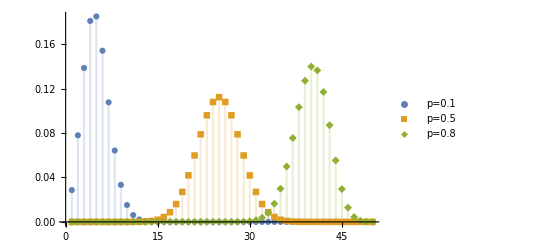

```mathematica
DiscretePlot[Table[PDF[BinomialDistribution[50,p],k],{p,{0.1,0.5,0.8}}]//Evaluate,{k,50},PlotRange->All,PlotMarkers->Automatic, PlotLegends->{"p=0.1","p=0.5","p=0.8"}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/binomial_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\binomial_distribution.pdf

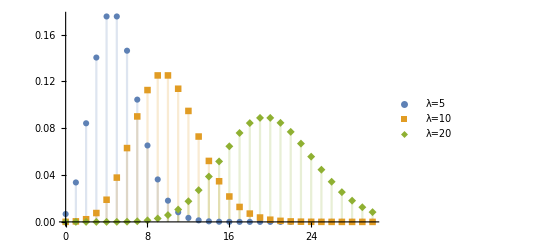

```mathematica
DiscretePlot[Table[PDF[PoissonDistribution[λ],k],{λ,{5,10,20}}]//Evaluate,{k,0,30},PlotRange->All,PlotMarkers->Automatic,PlotLegends->{"λ=5","λ=10", "λ=20"}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/poisson_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\poisson_distribution.pdf

```mathematica
GraphicsRow[Table[DiscretePlot3D[PDF[MultinomialDistribution[n,{0.6,0.4}],{x,y}],{y,0,n},{x,0,n},PlotLabel->Row[{"n = ",n}],ExtentSize->0.5],{n,{3,6, 9}}], ImageSize->Full]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/multinomial_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\multinomial_distribution.pdf

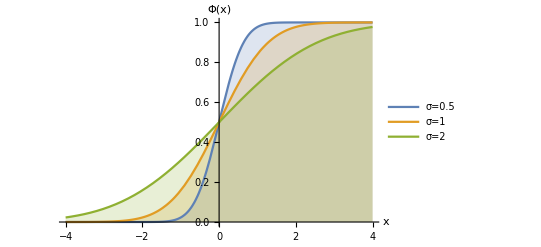

```mathematica
Plot[Table[CDF[NormalDistribution[0, σ],x],{σ,{0.5, 1,2}}]//Evaluate,{x,-4,4},AxesLabel->{"x","Φ(x)"},Filling->Axis,PlotLegends->Placed[{"σ=0.5","σ=1","σ=2"},Right]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/cumulative_normal_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\cumulative_normal_distribution.pdf

```mathematica
Probability[x,x\[Distributed]NormalDistribution[]]
```

```mathematica
Probability[x ≤ 0,x\[Distributed]NormalDistribution[0,1]]
```

1/2

```mathematica
CDF[NormalDistribution[],0]
```

1/2

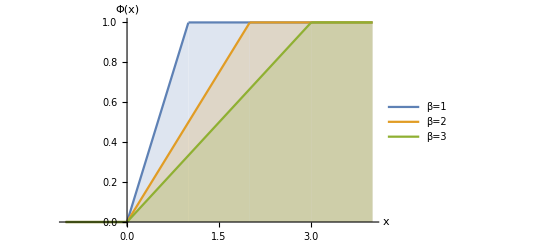

```mathematica
Plot[Table[CDF[UniformDistribution[{0, β}],x],{β,{1, 2,3}}]//Evaluate,{x,-1,4},AxesLabel->{"x","Φ(x)"},Filling->Axis,PlotLegends->Placed[{"β=1","β=2","β=3"},Right]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/cumulative_uniform_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\cumulative_uniform_distribution.pdf

```mathematica
MarginalDistribution[MultinormalDistribution[{0,0},{{2,1},{1,2}}], 1]
```

NormalDistribution[0,√2]

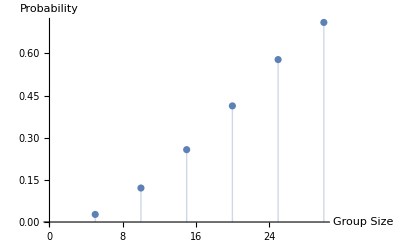

```mathematica
(* Double Birthday Problem *)
birthdays=Range[365];
sameBirthdaysInGroup[n_Integer]:=Module[{sameBirthday,groupSamples,sampleSize=10000},groupSamples=RandomChoice[birthdays,{sampleSize,n}];
sameBirthday=Map[Boole[MemberQ[Differences[Sort[#]],0]]&,groupSamples];
Return[Apply[Plus,sameBirthday]/sampleSize //N]];
groupSizes ={5,10,15,20,25,30};
probs = Map[sameBirthdaysInGroup, groupSizes];
ListPlot[Transpose[{groupSizes,probs}],Filling->Axis, AxesLabel->{"Group Size","Probability"}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/double_birthday_problem.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\double_birthday_problem.pdf

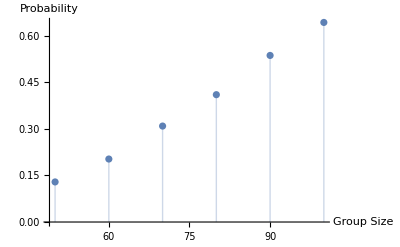

```mathematica
(* Triple Birthday Problem *)
birthdays=Range[365];
SameBirthdaysInGroup[n_Integer]:=Module[{sameBirthday,groupSamples,sampleSize=10000},groupSamples=RandomChoice[birthdays,{sampleSize,n}];
sameBirthday=Map[Boole[MemberQ[Partition[Differences[Sort[#]],2,1],{0,0}]]&,groupSamples];
Return[Apply[Plus,sameBirthday]/sampleSize //N]];
groupSizes ={50, 60, 70, 80, 90, 100};
probs = Map[SameBirthdaysInGroup, groupSizes];
ListPlot[Transpose[{groupSizes,probs}],Filling->Axis, AxesLabel->{"Group Size","Probability"}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/triple_birthday_problem.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\triple_birthday_problem.pdf

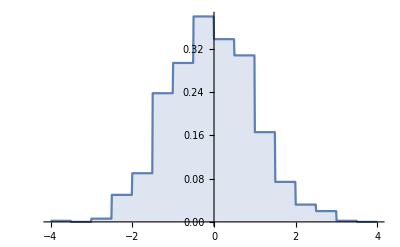

```mathematica
data=RandomVariate[NormalDistribution[],1000];
dist=HistogramDistribution[data];
DiscretePlot[PDF[dist,x],{x,-4,4,.01}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/histogram_distribution.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\histogram_distribution.pdf

```mathematica
data=RandomVariate[NormalDistribution[0,1],1000];
dist=EstimatedDistribution[data,NormalDistribution[μ,σ],ParameterEstimator->"MaximumLikelihood"]
```

NormalDistribution[0.0400075,0.974344]

```mathematica
{Mean[data],StandardDeviation[data],RootMeanSquare[data-Mean[data]]}
```

{0.0400075,0.974832,0.974344}

```mathematica
RootMeanSquare[data-Mean[data]]*Sqrt[1000/999]==StandardDeviation[data]
```

True

```mathematica
FindDistribution[data]
```

NormalDistribution[0.0400075,0.974344]

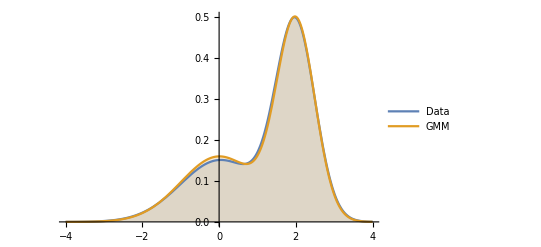

```mathematica
mixture= MixtureDistribution[{0.4,0.6},{NormalDistribution[],NormalDistribution[2,0.5]}];data=RandomVariate[mixture,1000];
dist=LearnDistribution[data,Method->"GaussianMixture"];
Plot[{PDF[dist,x], PDF[mixture,x]},{x,-4,4},Filling->Axis,PlotLegends->Placed[{"Data","GMM"},Right]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/gaussian_mixture_model.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\gaussian_mixture_model.pdf

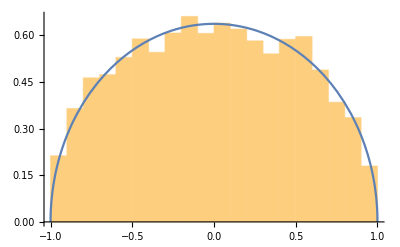

```mathematica
pmax=2/Pi;
SemiCircleDistribution[x_]:=pmax*Sqrt[1-x^2];
xk=RandomVariate[UniformDistribution[{-1,1}],10000];
rk=RandomVariate[UniformDistribution[{0,1}],10000];
data =Pick[xk, MapThread[#1<(SemiCircleDistribution[#2]/pmax)&,{rk,xk}]];
Show[{Histogram[data, 20, "PDF"],Plot[SemiCircleDistribution[x],{x,-1,1}]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/rejection_sampling.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\rejection_sampling.pdf

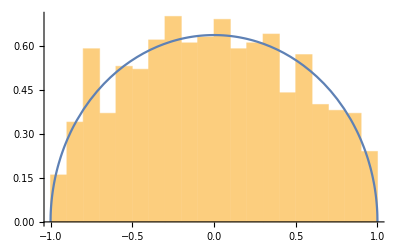

```mathematica
dist=ProbabilityDistribution[SemiCircleDistribution[x],{x,-1,+1}];
data = RandomVariate[dist, 1000];
Show[{Histogram[data, 20, "PDF"],Plot[SemiCircleDistribution[x],{x,-1,1}]}]
```

{3.,Null}

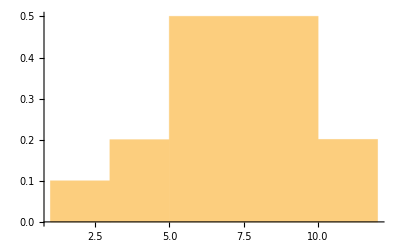

```mathematica
sampleFromHistogram[bins_,binHeights_,numSamples_]:=Module[{cumSum,randomNumbers,binIndices,histSamples},
cumSum=Prepend[Accumulate[binHeights],0];
randomNumbers=RandomReal[1,numSamples];
binIndices=Flatten[Map[Ordering[Select[cumSum-#,NonPositive],-1]&,randomNumbers]];
histSamples=Map[RandomReal[{bins[[#]],bins[[#+1]]}]&,binIndices];
Return[histSamples]]

Timing[data=sampleFromHistogram[{1,3,5,10,12},{0.1,0.2,0.5,0.2},1000000];]
Histogram[data,{{1,3,5,10,12}},"Probability"]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/histogram_sampling.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\histogram_sampling.pdf

{0.03125,Null}

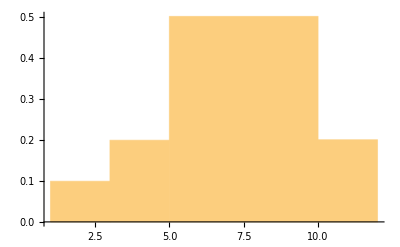

```mathematica
dist = HistogramDistribution[data,{{1,3,5,10,12}}];
Timing[data2 = RandomVariate[dist, 1000000];]
Histogram[data2,{{1,3,5,10,12}},"Probability"]
```

```mathematica
sampleFromGaussianMixtureModel[weights_,means_,covariances_,numSamples_]:=Module[{distributions,mixture,samples},distributions=If[NumberQ[means[[1]]],MapThread[NormalDistribution[#1,#2]&,{means,covariances}],MapThread[MultinormalDistribution[#1,#2]&,{means,covariances}]];
mixture=MixtureDistribution[weights,distributions];
samples=RandomVariate[mixture,numSamples];
Return[samples]]
```

```mathematica
sampleFromGaussianMixtureModel[{0.5,0.5},{{1,1}, {2,2}}, {{{1,0},{0,1}},{{1,0},{0,1}}},10]
```

{{1.77218,1.96591},{3.79929,-0.177864},{0.260659,0.479329},{0.573208,0.753695},{0.357539,1.41841},{2.09129,3.17798},{1.0092,1.03106},{2.07979,-0.600844},{2.9402,0.861611},{1.4713,2.33864}}

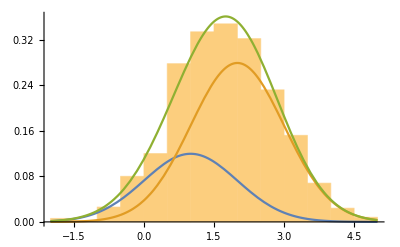

```mathematica
data =sampleFromGaussianMixtureModel[{0.3,0.7},{1, 2}, {1,1},1000];
Show[{Histogram[data, 20, "PDF"],Plot[{0.3*PDF[NormalDistribution[1,1],x],
0.7*PDF[NormalDistribution[2,1],x],0.3*PDF[NormalDistribution[1,1],x]+0.7*PDF[NormalDistribution[2,1],x]},{x,-2,5}]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/gaussian_mixture_model_sampling.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\gaussian_mixture_model_sampling.pdf

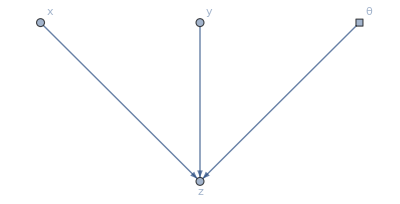

```mathematica
Graph[{1->3,2->3,4->3},VertexLabels->{1-> "x",2-> "y",3-> Placed["z", Below],4-> θ},VertexShapeFunction-> {4->"Square"},VertexSize->Tiny]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/simple_graph.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\simple_graph.pdf

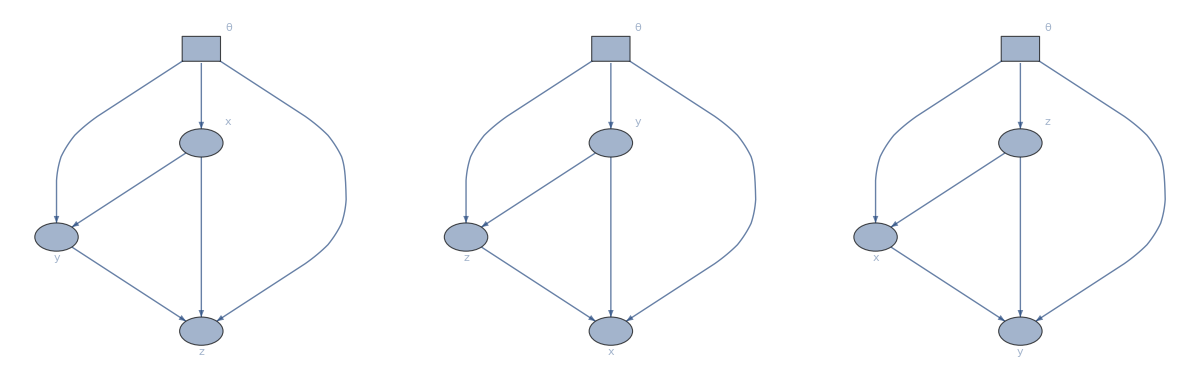

```mathematica
GraphicsRow[{Graph[{1->3,2->3,4->3,4->2,4->1,1->2},VertexLabels->{1-> "x",2-> Placed["y",Below],3-> Placed["z", Below],4-> θ},VertexShapeFunction-> {4->"Square"},VertexSize->0.3],
Graph[{2->1,3->1,2->3,4->3,4->2,4->1},VertexLabels->{1-> Placed["x", Below],2->"y",3-> Placed["z", Below],4-> θ},VertexShapeFunction-> {4->"Square"},VertexSize->0.3],
Graph[{1->2,3->2,3->1,4->3,4->2,4->1},VertexLabels->{1-> Placed["x", Below],2->Placed["y",Below],3-> "z",4-> θ},VertexShapeFunction-> {4->"Square"},VertexSize->0.3]}
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/decomposition_graphs.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\decomposition_graphs.pdf

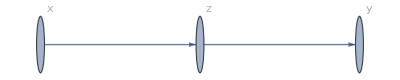

```mathematica
Graph[{1->3,3->2},VertexLabels->{1-> "x",2-> "y",3-> "z"},VertexSize->Tiny]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/graph_example.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\graph_example.pdf

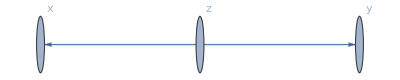

```mathematica
Graph[{3->1,3->2},VertexLabels->{1-> "x",2-> "y",3-> "z"},VertexSize->Tiny, VertexCoordinates->{3->{0,0},1-> {-1,0},2-> {1,0}}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/graph_exercise.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\graph_exercise.pdf

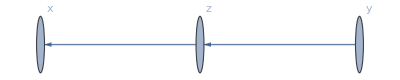

```mathematica
Graph[{2->3,3->1},VertexLabels->{1-> "x",2-> "y",3-> "z"},VertexSize->Tiny,VertexCoordinates->{3->{0,0},1-> {-1,0},2-> {1,0}}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/equivalent_graph.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\equivalent_graph.pdf

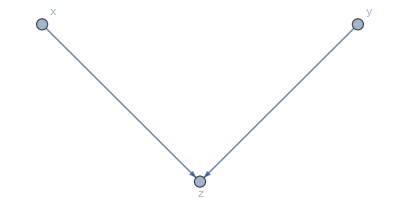

```mathematica
Graph[{1->3,2->3},VertexLabels->{1-> "x",2-> "y",3-> Placed["z", Below]},VertexCoordinates->{3->{0,0},1-> {-1,1},2-> {1,1}},VertexSize->Tiny]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/v_structure.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\v_structure.pdf

```mathematica
IsConditionalIndependent[g_Graph,sourceNode_Integer,targetNode_Integer,conditionalNodes_List]:=Module[{paths, blockedPathSegments},
(* source and target node are identical *)
If[sourceNode ==targetNode, Return[False]];
paths = FindPath[UndirectedGraph[g],sourceNode,targetNode, Infinity,All];
(* there is a direct path between source and target node *)
If[AnyTrue[paths,Length[#]==2&], Return[False]];
(* there is no path between source and target node *)
If[Length[paths]==0 , Return[True]];
(* partition each path into overlapping segments of 3 nodes *)
paths = Map[Partition[#,3,1]&,paths];
(* get all paths, which are not blocked by a a conditional node *)
blockedPathSegments =Map[Not[EdgeQ[g,#[[1]] ->#[[2]]] && EdgeQ[g,#[[3]] ->#[[2]]]] && MemberQ[conditionalNodes,#[[2]]]  &, paths, {2}];
paths = Pick[paths,Map[Not[AnyTrue[#,TrueQ]]&,blockedPathSegments]];
If[Length[paths]==0 , Return[True]];
(* get all paths, which are not blocked by a v-structure *)
blockedPathSegments =Map[EdgeQ[g,#[[1]] ->#[[2]]] && EdgeQ[g,#[[3]] ->#[[2]]]&& Not[MemberQ[conditionalNodes,#[[2]]]]  && Length[Intersection[VertexOutComponent[g,#[[2]]], conditionalNodes]]==0 &, paths, {2}];
paths = Pick[paths,Map[Not[AnyTrue[#, TrueQ]]&,blockedPathSegments]];
If[Length[paths]==0 , Return[True], Return[False]];
]
```

```mathematica
g =Graph[{1 -> 3, 2 -> 3,3 -> 4}, VertexLabels->{1-> "x",2-> "y",3-> "z", 4 -> "w"}];
IsConditionalIndependent[g, 1, 2, {4}]
```

False

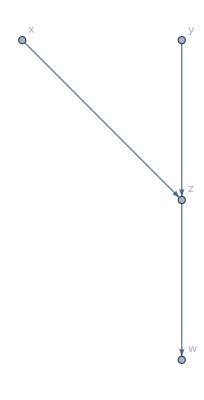

```mathematica
g
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/v_structure_with_descendant.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\v_structure_with_descendant.pdf

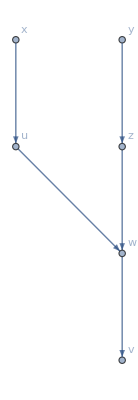

```mathematica
g=Graph[{1 -> 5, 2 -> 3,3 -> 4,5-> 4,4 -> 6}, VertexLabels->{1-> "x",2-> "y",3-> "z", 4 -> "w",5-> "u", 6-> "v"}];
g
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/complex_graph.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\complex_graph.pdf

```mathematica
AbsoluteTime["01 Jan 1970 00:00:00.000"]-AbsoluteTime["01 Jan 1970 00:00:00.000", TimeZone-> 0]
```

7200

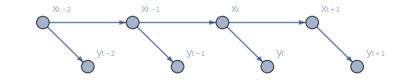

```mathematica
Graph[{1->2,1->3,3->4,3->5,5->6,5->7,7->8},VertexLabels->{1-> Subscript["x","t-2"],2-> Subscript["y","t-2"],3-> Subscript["x","t-1"],4-> Subscript["y","t-1"],5-> Subscript["x","t"],6-> Subscript["y","t"],7-> Subscript["x","t+1"],8-> Subscript["y","t+1"]},VertexSize->0.2,VertexCoordinates->Table[{i,Mod[i,2]},{i,1,8}]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/time_series_graph.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\time_series_graph.pdf

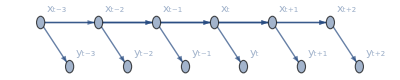

```mathematica
g1=Graph[{1->2,1->3,3->4,3->5,5->6,5->7,7->8,7->9, 9->10,9->11,11->12,1->5,3->7,5->9,7->11},VertexLabels->{1-> Subscript["x","t-3"],2-> Subscript["y","t-3"],3-> Subscript["x","t-2"],4-> Subscript["y","t-2"],5-> Subscript["x","t-1"],6-> Subscript["y","t-1"],7-> Subscript["x","t"],8-> Subscript["y","t"],,9-> Subscript["x","t+1"],10-> Subscript["y","t+1"],11-> Subscript["x","t+2"],12-> Subscript["y","t+2"]},VertexSize->0.2,VertexCoordinates->Table[{i,Mod[i,2]},{i,1,12}]]
```

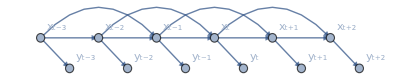

```mathematica
g2=SetProperty[{g1,1->5},EdgeShapeFunction->({Arrow[GraphElementData[{"CurvedArc","Curvature"->1}][##]]}&)];
g3=SetProperty[{g2,3->7},EdgeShapeFunction->({Arrow[GraphElementData[{"CurvedArc","Curvature"->1}][##]]}&)];
g4=SetProperty[{g3,5->9},EdgeShapeFunction->({Arrow[GraphElementData[{"CurvedArc","Curvature"->1}][##]]}&)];
SetProperty[{g4,7->11},EdgeShapeFunction->({Arrow[GraphElementData[{"CurvedArc","Curvature"->1}][##]]}&)]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/non_markov_graph.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\non_markov_graph.pdf

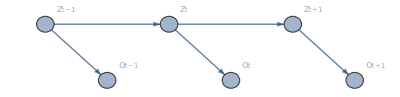

```mathematica
Graph[{1->2,1->3,3->4,3->5,5->6},VertexLabels->{1-> Subscript["z","t-1"],2-> Subscript["o","t-1"],3->Subscript["z","t"],4-> Subscript["o","t"],5-> Subscript["z","t+1"],6-> Subscript["o","t+1"]},VertexSize->0.2,VertexCoordinates->Table[{i,Mod[i,2]},{i,1,6}]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/markov_graph.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\markov_graph.pdf

```mathematica
GraphWorld[nodeLabels_List,historyLength_Integer]:=Module[
{graph, transitionMatrix, history, world, numNodes, labels, initialState, nodes, dists, edges, historyGraph},
numNodes =Length[nodeLabels];
nodes = Range[numNodes];
labels =MapThread[#1-> #2&,{nodes,nodeLabels}];
transitionMatrix = RandomChoice[{0,1},{numNodes, numNodes}];
(* There could be a row with only zeros, where no transitions to another node occurs.
To avoid this situation, a random unit vector will replace such a row. *)
transitionMatrix =Map[If[Total[#]==0,UnitVector[Length[#],RandomChoice[nodes]],#]&,transitionMatrix];
graph = AdjacencyGraph[transitionMatrix, VertexLabels-> labels];
transitionMatrix = Map[#/Total[#]&,transitionMatrix];
initialState = RandomChoice[nodes];
dists = Map[EmpiricalDistribution[#->nodes]&,transitionMatrix];
history = NestList[RandomVariate[dists[[#]]]&,initialState, historyLength];
edges = Partition[history,2,1];
historyGraph=Graph[Table[Labeled[i->i+1,i],{i,1,Length[edges]}],
VertexLabels->Append[Table[i->nodeLabels[[edges[[i,1]]]],{i,1,Length[edges]}],
Length[edges]+1->nodeLabels[[edges[[Length[edges],2]]]]]];
world= Association["graph"-> graph, 
                                        "transition_probabilities" -> Transpose[transitionMatrix],
                                        "history"-> history ,
                                        "timeline"-> historyGraph];
Return[world]]
```

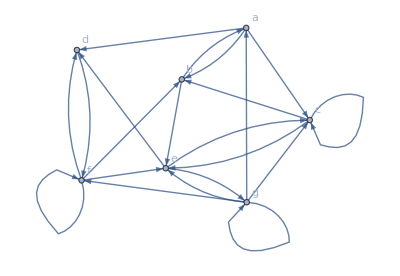

```mathematica
SeedRandom[123456789];
world=GraphWorld[Characters["abcdefg"],10];
world["graph"]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/graph_world.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\graph_world.pdf

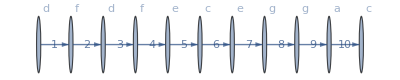

```mathematica
world["timeline"]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/state_history.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\state_history.pdf

```mathematica
MeasurementProcess[world_,observerNode_]:=Module[{measurements,distances,size,dist},(*Calculate a list with the number of edges in the shortest path between the observer node and all the system states in the world's history.*)measurements=Map[GraphDistance[world["graph"],observerNode,#]&,world["history"][[2;;All]]];
(*Calculate the graph distances between the observer node and all other graph nodes.*)distances=GraphDistance[world["graph"],observerNode];
size=Length[distances];
(*Calculate the measurement distribution for each time step by checking,which node has the same graph distance than the measurement and normalize them.*)dist=Boole[Map[MapThread[Equal,{distances,Table[#,size]}]&,measurements]];
dist=Map[#/Total[#]&,dist];
Return[dist]]

measurements=MeasurementProcess[world,2]
```

{{0,0,0,0,0,1,0},{0,0,1/3,1/3,0,0,1/3},{0,0,0,0,0,1,0},{1/2,0,0,0,1/2,0,0},{0,0,1/3,1/3,0,0,1/3},{1/2,0,0,0,1/2,0,0},{0,0,1/3,1/3,0,0,1/3},{0,0,1/3,1/3,0,0,1/3},{1/2,0,0,0,1/2,0,0},{0,0,1/3,1/3,0,0,1/3}}

```mathematica
nodes=Characters["abcdefg"];
stateDistribution=AssociationThread[nodes->Table[1/Length[nodes],Length[nodes]]];
stateDistribution=AssociationThread[nodes->world["transition_probabilities"].Values[stateDistribution]];
stateDistribution=AssociationThread[nodes->measurements[[1]]*Values[stateDistribution]];
stateDistribution=If[Total[stateDistribution]==0,AssociationThread[nodes->Table[1/Length[nodes],Length[nodes]]],stateDistribution/Total[stateDistribution]];
ListPlot[stateDistribution,Filling->Axis, AxesLabel->{"Vertex","Probability"}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/state_estimate_t1.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\state_estimate_t1.pdf

```mathematica
stateDistribution=AssociationThread[nodes->world["transition_probabilities"].Values[stateDistribution]];
stateDistribution=AssociationThread[nodes->measurements[[2]]*Values[stateDistribution]];
stateDistribution=If[Total[stateDistribution]==0,AssociationThread[nodes->Table[1/Length[nodes],Length[nodes]]],stateDistribution/Total[stateDistribution]];
ListPlot[stateDistribution,Filling->Axis, AxesLabel->{"Vertex","Probability"}, PlotRange->{{0,7.5},{0,1}}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/state_estimate_t2.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\state_estimate_t2.pdf

```mathematica
stateDistribution=AssociationThread[nodes->world["transition_probabilities"].Values[stateDistribution]];
stateDistribution=AssociationThread[nodes->measurements[[3]]*Values[stateDistribution]];
stateDistribution=If[Total[stateDistribution]==0,AssociationThread[nodes->Table[1/Length[nodes],Length[nodes]]],stateDistribution/Total[stateDistribution]];
ListPlot[stateDistribution,Filling->Axis, AxesLabel->{"Vertex","Probability"}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/state_estimate_t3.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\state_estimate_t3.pdf

```mathematica
stateDistribution=AssociationThread[nodes->world["transition_probabilities"].Values[stateDistribution]];
stateDistribution=AssociationThread[nodes->measurements[[4]]*Values[stateDistribution]];
stateDistribution=If[Total[stateDistribution]==0,AssociationThread[nodes->Table[1/Length[nodes],Length[nodes]]],stateDistribution/Total[stateDistribution]];
ListPlot[stateDistribution,Filling->Axis, AxesLabel->{"Vertex","Probability"}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/state_estimate_t4.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\state_estimate_t4.pdf

```mathematica
stateDistribution=AssociationThread[nodes->world["transition_probabilities"].Values[stateDistribution]];
stateDistribution=AssociationThread[nodes->measurements[[5]]*Values[stateDistribution]];
stateDistribution=If[Total[stateDistribution]==0,AssociationThread[nodes->Table[1/Length[nodes],Length[nodes]]],stateDistribution/Total[stateDistribution]];
ListPlot[stateDistribution,Filling->Axis, AxesLabel->{"Vertex","Probability"}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/state_estimate_t5.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\state_estimate_t5.pdf

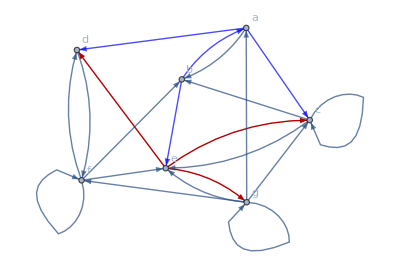

```mathematica
HighlightGraph[world["graph"],{5->4, 5->7,5->3, Style[2->1,Blue],Style[1->4,Blue],Style[1->3,Blue],Style[2->5,Blue]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/highlighted_graph_world.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\highlighted_graph_world.pdf

```mathematica
Trajectory[initialPosition_,initialSpeed_,initialTime_, numberOfCollisions_,boundaries_List:{+1,-1,+1,-1}]:=Module[{trajectory,Propagate},
Propagate[state_]:=Module[{collisionTimes,nextCollisionTime, t, newState,
verticalWallCollision, horizontalWallCollision},
collisionTimes=Association[1->(boundaries[[1]]-state["position"][[1]])/state["velocity"][[1]],2->(boundaries[[2]]-state["position"][[1]])/state["velocity"][[1]],3->(boundaries[[3]]-state["position"][[2]])/state["velocity"][[2]],4->(boundaries[[4]]-state["position"][[2]])/state["velocity"][[2]]];
nextCollisionTime=MinimalBy[Value]@Select[collisionTimes,# > 0.0000000000001&];
t = Values[nextCollisionTime][[1]];
newState = Association["time"->state["time"]+t,
"position"->state["position"]+state["velocity"]*t,
"velocity"->state["velocity"]];
verticalWallCollision =Boole[IntersectingQ[Keys[nextCollisionTime],{1,2}]];
horizontalWallCollision =Boole[IntersectingQ[Keys[nextCollisionTime],{3,4}]];
newState["velocity"]= {newState["velocity"][[1]] *(-1)^verticalWallCollision,
newState["velocity"][[2]] *(-1)^horizontalWallCollision};
Return[newState]];
trajectory=NestList[Propagate,Association["time"->initialTime,"position"->initialPosition,"velocity"->initialSpeed],numberOfCollisions];
Return[trajectory]]
```

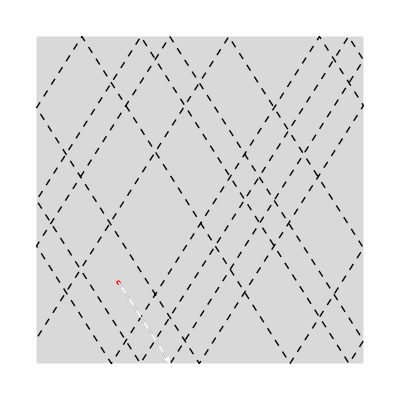

```mathematica
boundaries = {1,-1,1,-1};
initialVelocity = {1/Pi,-0.5};
trajectory=Trajectory[{-0.5,-0.5},initialVelocity,0,20, boundaries];
box=Polygon[{{1,1},{1,-1},{-1,-1},{-1,1}}];
ball=Point[trajectory[[1]]["position"]];
arrow=Arrow[{trajectory[[1]]["position"],trajectory[[2]]["position"]}];
track=Line[Map[#["position"]&,trajectory]];
Graphics[{{LightGray,box},{Dashed,track},{PointSize[Large],Red,ball},{White,arrow}}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/ball_trajectory.pdf"}],%]
```

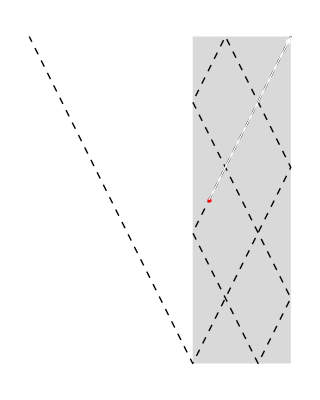

```mathematica
trajectory =Trajectory[{0,0},{0.1,0.2},0,9,{0.5,-0.1,1,-1}];
box = Polygon[{{0.5,1},{0.5,-1},{-0.1,-1},{-0.1,1}}];
ball = Point[trajectory[[1]]["position"]];
arrow = Arrow[{trajectory[[1]]["position"],trajectory[[2]]["position"]}];
track = Line[Map[#["position"]&,trajectory]];
Graphics[{{LightGray,box},{Dashed,track},{PointSize[Large],Red,ball},{White,arrow}}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/ball_escapes_box.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\ball_escapes_box.pdf

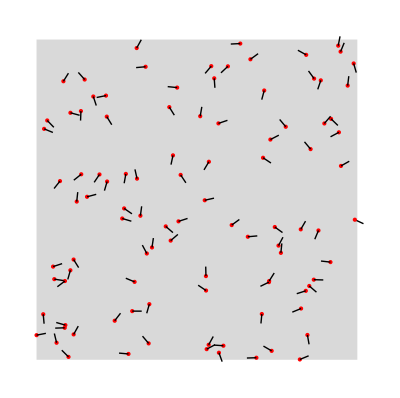

```mathematica
numberOfParticles=100;
pos=Transpose[{RandomVariate[UniformDistribution[{boundaries[[1]],boundaries[[2]]}],numberOfParticles],RandomVariate[UniformDistribution[{boundaries[[3]],boundaries[[4]]}],numberOfParticles]}];
v0=Sqrt[initialVelocity.initialVelocity];
vel=Map[v0*{Cos[#],Sin[#]}&,RandomVariate[UniformDistribution[{0,2*Pi}],numberOfParticles]];
particles=MapThread[Association["position"->#1,"velocity"->#2]&,{pos,vel}];
points=Point[Map[#["position"]&,particles]];
directions=Map[Line[{#["position"],#["position"]+#["velocity"]*0.1}]&,particles];
Graphics[{{LightGray,box},{PointSize[Large],Red,points}, directions}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"images/particles.pdf"}],%]
```

C:\Users\gerha\My Projects\Book\Probabilistic Modeling with the Wolfram Language\images\particles.pdf